Your Title Here

```mathematica
w1=5;w2=7;h1=3;h2=5;L=2*(w1+w2);H=h1+h2;
```

```mathematica
truss=Graphics[{Thick,
{Thickness@#1,#2,Line[{{w2,0},{0.67*w2,h1}}],Line[{{w2,0},{w1+w2,H}}],Line[{{2*w1+w2,0},{L-0.67*w2,h1}}],Line[{{2*w1+w2,0},{w1+w2,H}}],Line[{{w1+w2,0},{w1+w2,H}}],
EdgeForm@{Thickness@#1,#2},FaceForm@None,Polygon[{{0,0},{L,0},{w1+w2,H}}]}&@@@{{0.015,Black},{0.01,GrayLevel@0.8}},

{GrayLevel@0.7,
Polygon[{{-0.7,-1},{0.7,-1},{0.5,0},{-0.5,0}}],Disk[{0,0},0.5],
Disk[{L,0},0.3],Disk[{L,-0.5},0.5],Polygon[{{L-0.275,0.12},{L+0.275,0.12},{L+0.47,-0.33},{L-0.47,-0.33}}]
},
{Thin,Line[{{-0.5,0},{-0.7,-1},{0.7,-1},{0.5,0}}],Line[{#,√(0.5^2-#^2)}&/@Range[-0.5,0.5,0.02]],
Line[{{L+#*0.275,0.12},{L+#*0.47,-0.33}}]&/@{-1,1},
Line[{#,√(0.3^2-(#-L)^2)}&/@Range[L-0.275,L+0.275,0.01]],Line[{#,-√(0.5^2-(#-L)^2)-0.5}&/@Range[L-0.5,L+0.5,0.01]],
Line[{#,√(0.5^2-(#-L)^2)-0.5}&/@Range[L-0.5,L-0.47,0.01]],Line[{#,√(0.5^2-(#-L)^2)-0.5}&/@Range[L+0.47,L+0.5,0.01]],
Line[{{#-1,-1},{#+1,-1}}]&/@{0,L}},

{PointSize@0.01,Point@{#,0}}&/@{0,L}

},ImageSize->{600,400}];
```

```mathematica
Manipulate[
Module[{θ1,scale},
θ1=ArcTan[h1/(0.33*w2)];
scale[F_]:=1.5+5*Rescale[F,{0,10}];

Show[truss,PlotRange->{-1.15,15.8},Epilog->{Thick,Arrowheads@0.045,
{Blue,Arrow[{{0.67*w2-scale[FA]*Cos[θ1],h1+scale[FA]*Sin[θ1]},{0.67*w2,h1}}],Arrow[{{w1+w2,h1+h2+scale[FB]},{w1+w2,h1+h2}}],
Text[Style[Row@{Subscript[Style["F",Italic],#1]," = ",NumberForm[#2,{3,1}]," kN"},18,Blue],#3,#4]&@@@{{"A",FA,{0.67*w2-scale[FA]*Cos[θ1],h1+scale[FA]*Sin[θ1]},{0.,-1}},{"B",FB,{w1+w2,h1+h2+scale[FB]},{0,-1.5}}}}
}]
],
Grid[{
{Control[{{member,1,"member"},{1->" 1 ",2->" 2 ",3->" 3 ",4->" 4 ",5->" 5 ",6->" 6 ",7->" 7 ",8->" 8 "},Setter}],SpanFromLeft},
{Style["point load forces (kN)",Bold],
Control[{{FA,2,"diagonal"},0,5,0.1,Appearance->"Labeled",ImageSize->Small}],
Control[{{FB,5,"vertical"},0,10,0.1,Appearance->"Labeled",ImageSize->Small}]}
},Alignment->Left],
SaveDefinitions->True]
```

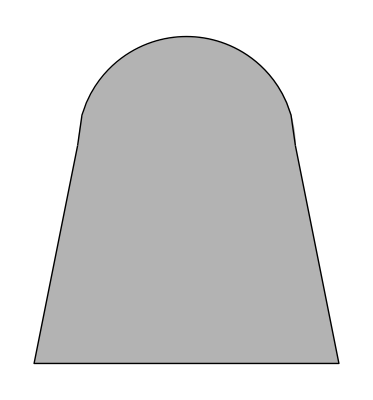

```mathematica
Graphics[{
{GrayLevel@0.7,Polygon[{{-0.7,-1},{0.7,-1},{0.5,0},{-0.5,0}}],Disk[{0,0},0.5]},
Thick,Line[{{-0.5,0},{-0.7,-1},{0.7,-1},{0.5,0}}],Line[{#,√(0.5^2-#^2)}&/@Range[-0.5,0.5,0.02]]
}]
```

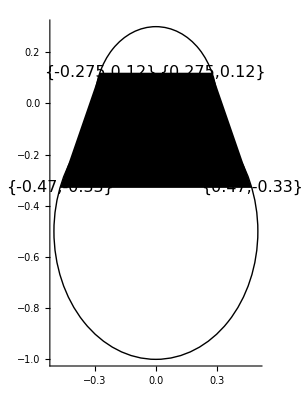

```mathematica
Module[{L,r1,r2},
L=0;r1=0.3;r2=0.5;

Graphics[{
Circle[{L,0},r1],Circle[{L,-r2},r2],
(*Line[{{-0.275,0.12},{-0.47,-0.33}}],
Line[{{0.275,0.12},{0.47,-0.33}}],*)
Polygon[{{-0.275,0.12},{0.275,0.12},{0.47,-0.33},{-0.47,-0.33}}],
Text[Style[#,16,Black,Background->White],#]&/@{{-0.275,0.12},{0.275,0.12},{0.47,-0.33},{-0.47,-0.33}}
(*{Polygon[#],Red,PointSize@0.02,Point@#}&/@{{-0.275,0.12},{0.275,0.12},{0.47,-0.33},{-0.47,-0.33}}*)
},Axes->True]
]
```

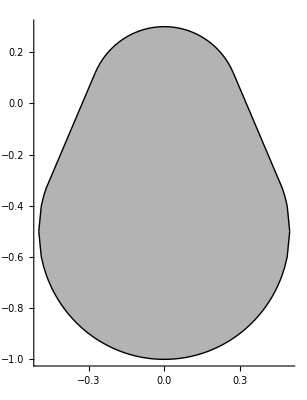

```mathematica
Module[{L},
L=0;

Graphics[{
{GrayLevel@0.7,Disk[{L,0},0.3],Disk[{L,-0.5},0.5],Polygon[{{L-0.275,0.12},{L+0.275,0.12},{L+0.47,-0.33},{L-0.47,-0.33}}]},
Line[{{L+#*0.275,0.12},{L+#*0.47,-0.33}}]&/@{-1,1},
Line[{#,√(0.3^2-(#-L)^2)}&/@Range[L-0.275,L+0.275,0.01]],Line[{#,-√(0.5^2-(#-L)^2)-0.5}&/@Range[L-0.5,L+0.5,0.01]],
Line[{#,√(0.5^2-(#-L)^2)-0.5}&/@Range[L-0.5,L-0.47,0.01]],Line[{#,√(0.5^2-(#-L)^2)-0.5}&/@Range[L+0.47,L+0.5,0.01]]
},Axes->True](*;
{#,√(0.5^2-(#-L))}&/@Range[L-0.47,L+0.25,0.01]*)
]
```

```mathematica
#&/@{{0,0},{1,1},{2,2}}
```

{{0,0},{1,1},{2,2}}

```mathematica
3*1.27/0.8
```

4.7625

```mathematica
4.762/7
```

0.680286

```mathematica
√(1.5^2-0.8^2)
```

1.26886

```mathematica
N@4/7
```

0.571429

0.667656





```mathematica
Module[{w1,w2,h1,h2,y1,y2,x0},
w1=5;w2=7;h1=3;h2=5;

y1[x_]:=(h1+h2)/(w1+w2)*x;
y2[x_]:=h1/(0.68*w2-w2)*(x-w2);

x0=x/.Quiet@Solve[y1[x]==y2[x],x][[1]];
x0/w2
]
```

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

Contributed by: XXXX